```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dat = Import["temp.csv","Table"];
```

```mathematica
min = Min[dat];
sum = Total[dat-min,2];
p = (dat-min)/sum;
```

```mathematica
{m,n}=Dimensions[p];
mean=Sum[{i,j} p[[i,j]],{i,1,m},{j,1,n}];
cov=Sum[Outer[Times,{i,j}-mean,{i,j}-mean] p[[i,j]],{i,1,m},{j,1,n}];
```

```mathematica
cov
```

{{7177.99,-28.3953},{-28.3953,6166.16}}

```mathematica
f[i_,j_]:=Evaluate[PDF[MultinormalDistribution[mean,cov],{i,j}]];
g[i_,j_]:=f[i,j]sum+min;
```

```mathematica
ListPlot3D[dat,PlotRange->All]
Plot3D[g[i,j],{i,1,m},{j,1,n}]
```

-Graphics3D-

-Graphics3D-

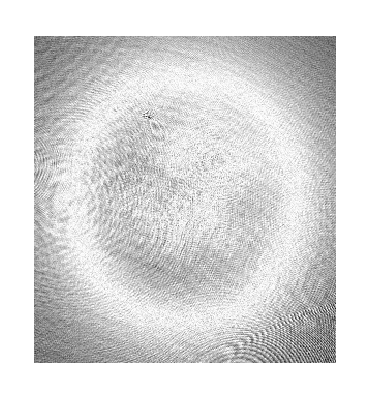

```mathematica
ArrayPlot[dat-Table[g[i,j],{i,1,m},{j,1,n}]]
```

```mathematica
dat-Table[g[i,j],{i,1,m},{j,1,n}]
```

{{0.493371,0.488215,0.606038,0.479842,0.558625,0.618388,«280»,0.445706,0.411063,0.470399,0.641716,0.597011,0.596286},«314»,{«1»}}

```mathematica
mean
```

{1643.01,1556.42}

```mathematica
λ=0.461;
pixelSize=8;
```

```mathematica
Total[dat,2]*2π*pixelSize^2/(3 λ^2)
```

3.91336×10^6